```mathematica
Sum[k^2,{k,1,n}]
```

1/6 n (1+n) (1+2 n)

```mathematica
1/6 n (1+n) (1+2 n)/.n->3
```

14

```mathematica
1^2+2^2+3^2
```

14

```mathematica
r=5
```

5

```mathematica
?RandomInteger
```

```mathematica
A = Table[ RandomInteger[{1,r}],3,3]
B = Table[ RandomInteger[{1,r}],3,3]
```

{{1,3,5},{4,2,5},{5,2,4}}

{{2,5,2},{3,5,2},{5,5,2}}

```mathematica
A.B
```

{{36,45,18},{39,55,22},{36,55,22}}

```mathematica
B.A
```

{{32,20,43},{33,23,48},{35,29,58}}

```mathematica
?For
```

```mathematica
?While
```

```mathematica
?Table
```

```mathematica
A={1,2,3};
Subsets[A]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
A=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Length[Subsets[A]]
```

1024

```mathematica
Subsets[A]
```

{{},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,7},{1,6,8},{1,6,9},{1,6,10},{1,7,8},{1,7,9},{1,7,10},{1,8,9},{1,8,10},{1,9,10},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,9},{2,4,10},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,10},{2,6,7},{2,6,8},{2,6,9},{2,6,10},{2,7,8},{2,7,9},{2,7,10},{2,8,9},{2,8,10},{2,9,10},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,4,9},{3,4,10},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{3,5,10},{3,6,7},{3,6,8},{3,6,9},{3,6,10},{3,7,8},{3,7,9},{3,7,10},{3,8,9},{3,8,10},{3,9,10},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{4,5,10},{4,6,7},{4,6,8},{4,6,9},{4,6,10},{4,7,8},{4,7,9},{4,7,10},{4,8,9},{4,8,10},{4,9,10},{5,6,7},{5,6,8},{5,6,9},{5,6,10},{5,7,8},{5,7,9},{5,7,10},{5,8,9},{5,8,10},{5,9,10},{6,7,8},{6,7,9},{6,7,10},{6,8,9},{6,8,10},{6,9,10},{7,8,9},{7,8,10},{7,9,10},{8,9,10},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7},{1,2,3,8},{1,2,3,9},{1,2,3,10},{1,2,4,5},{1,2,4,6},{1,2,4,7},{1,2,4,8},{1,2,4,9},{1,2,4,10},{1,2,5,6},{1,2,5,7},{1,2,5,8},{1,2,5,9},{1,2,5,10},{1,2,6,7},{1,2,6,8},{1,2,6,9},{1,2,6,10},{1,2,7,8},{1,2,7,9},{1,2,7,10},{1,2,8,9},{1,2,8,10},{1,2,9,10},{1,3,4,5},{1,3,4,6},{1,3,4,7},{1,3,4,8},{1,3,4,9},{1,3,4,10},{1,3,5,6},{1,3,5,7},{1,3,5,8},{1,3,5,9},{1,3,5,10},{1,3,6,7},{1,3,6,8},{1,3,6,9},{1,3,6,10},{1,3,7,8},{1,3,7,9},{1,3,7,10},{1,3,8,9},{1,3,8,10},{1,3,9,10},{1,4,5,6},{1,4,5,7},{1,4,5,8},{1,4,5,9},{1,4,5,10},{1,4,6,7},{1,4,6,8},{1,4,6,9},{1,4,6,10},{1,4,7,8},{1,4,7,9},{1,4,7,10},{1,4,8,9},{1,4,8,10},{1,4,9,10},{1,5,6,7},{1,5,6,8},{1,5,6,9},{1,5,6,10},{1,5,7,8},{1,5,7,9},{1,5,7,10},{1,5,8,9},{1,5,8,10},{1,5,9,10},{1,6,7,8},{1,6,7,9},{1,6,7,10},{1,6,8,9},{1,6,8,10},{1,6,9,10},{1,7,8,9},{1,7,8,10},{1,7,9,10},{1,8,9,10},{2,3,4,5},{2,3,4,6},{2,3,4,7},{2,3,4,8},{2,3,4,9},{2,3,4,10},{2,3,5,6},{2,3,5,7},{2,3,5,8},{2,3,5,9},{2,3,5,10},{2,3,6,7},{2,3,6,8},{2,3,6,9},{2,3,6,10},{2,3,7,8},{2,3,7,9},{2,3,7,10},{2,3,8,9},{2,3,8,10},{2,3,9,10},{2,4,5,6},{2,4,5,7},{2,4,5,8},{2,4,5,9},{2,4,5,10},{2,4,6,7},{2,4,6,8},{2,4,6,9},{2,4,6,10},{2,4,7,8},{2,4,7,9},{2,4,7,10},{2,4,8,9},{2,4,8,10},{2,4,9,10},{2,5,6,7},{2,5,6,8},{2,5,6,9},{2,5,6,10},{2,5,7,8},{2,5,7,9},{2,5,7,10},{2,5,8,9},{2,5,8,10},{2,5,9,10},{2,6,7,8},{2,6,7,9},{2,6,7,10},{2,6,8,9},{2,6,8,10},{2,6,9,10},{2,7,8,9},{2,7,8,10},{2,7,9,10},{2,8,9,10},{3,4,5,6},{3,4,5,7},{3,4,5,8},{3,4,5,9},{3,4,5,10},{3,4,6,7},{3,4,6,8},{3,4,6,9},{3,4,6,10},{3,4,7,8},{3,4,7,9},{3,4,7,10},{3,4,8,9},{3,4,8,10},{3,4,9,10},{3,5,6,7},{3,5,6,8},{3,5,6,9},{3,5,6,10},{3,5,7,8},{3,5,7,9},{3,5,7,10},{3,5,8,9},{3,5,8,10},{3,5,9,10},{3,6,7,8},{3,6,7,9},{3,6,7,10},{3,6,8,9},{3,6,8,10},{3,6,9,10},{3,7,8,9},{3,7,8,10},{3,7,9,10},{3,8,9,10},{4,5,6,7},{4,5,6,8},{4,5,6,9},{4,5,6,10},{4,5,7,8},{4,5,7,9},{4,5,7,10},{4,5,8,9},{4,5,8,10},{4,5,9,10},{4,6,7,8},{4,6,7,9},{4,6,7,10},{4,6,8,9},{4,6,8,10},{4,6,9,10},{4,7,8,9},{4,7,8,10},{4,7,9,10},{4,8,9,10},{5,6,7,8},{5,6,7,9},{5,6,7,10},{5,6,8,9},{5,6,8,10},{5,6,9,10},{5,7,8,9},{5,7,8,10},{5,7,9,10},{5,8,9,10},{6,7,8,9},{6,7,8,10},{6,7,9,10},{6,8,9,10},{7,8,9,10},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,7},{1,2,3,4,8},{1,2,3,4,9},{1,2,3,4,10},{1,2,3,5,6},{1,2,3,5,7},{1,2,3,5,8},{1,2,3,5,9},{1,2,3,5,10},{1,2,3,6,7},{1,2,3,6,8},{1,2,3,6,9},{1,2,3,6,10},{1,2,3,7,8},{1,2,3,7,9},{1,2,3,7,10},{1,2,3,8,9},{1,2,3,8,10},{1,2,3,9,10},{1,2,4,5,6},{1,2,4,5,7},{1,2,4,5,8},{1,2,4,5,9},{1,2,4,5,10},{1,2,4,6,7},{1,2,4,6,8},{1,2,4,6,9},{1,2,4,6,10},{1,2,4,7,8},{1,2,4,7,9},{1,2,4,7,10},{1,2,4,8,9},{1,2,4,8,10},{1,2,4,9,10},{1,2,5,6,7},{1,2,5,6,8},{1,2,5,6,9},{1,2,5,6,10},{1,2,5,7,8},{1,2,5,7,9},{1,2,5,7,10},{1,2,5,8,9},{1,2,5,8,10},{1,2,5,9,10},{1,2,6,7,8},{1,2,6,7,9},{1,2,6,7,10},{1,2,6,8,9},{1,2,6,8,10},{1,2,6,9,10},{1,2,7,8,9},{1,2,7,8,10},{1,2,7,9,10},{1,2,8,9,10},{1,3,4,5,6},{1,3,4,5,7},{1,3,4,5,8},{1,3,4,5,9},{1,3,4,5,10},{1,3,4,6,7},{1,3,4,6,8},{1,3,4,6,9},{1,3,4,6,10},{1,3,4,7,8},{1,3,4,7,9},{1,3,4,7,10},{1,3,4,8,9},{1,3,4,8,10},{1,3,4,9,10},{1,3,5,6,7},{1,3,5,6,8},{1,3,5,6,9},{1,3,5,6,10},{1,3,5,7,8},{1,3,5,7,9},{1,3,5,7,10},{1,3,5,8,9},{1,3,5,8,10},{1,3,5,9,10},{1,3,6,7,8},{1,3,6,7,9},{1,3,6,7,10},{1,3,6,8,9},{1,3,6,8,10},{1,3,6,9,10},{1,3,7,8,9},{1,3,7,8,10},{1,3,7,9,10},{1,3,8,9,10},{1,4,5,6,7},{1,4,5,6,8},{1,4,5,6,9},{1,4,5,6,10},{1,4,5,7,8},{1,4,5,7,9},{1,4,5,7,10},{1,4,5,8,9},{1,4,5,8,10},{1,4,5,9,10},{1,4,6,7,8},{1,4,6,7,9},{1,4,6,7,10},{1,4,6,8,9},{1,4,6,8,10},{1,4,6,9,10},{1,4,7,8,9},{1,4,7,8,10},{1,4,7,9,10},{1,4,8,9,10},{1,5,6,7,8},{1,5,6,7,9},{1,5,6,7,10},{1,5,6,8,9},{1,5,6,8,10},{1,5,6,9,10},{1,5,7,8,9},{1,5,7,8,10},{1,5,7,9,10},{1,5,8,9,10},{1,6,7,8,9},{1,6,7,8,10},{1,6,7,9,10},{1,6,8,9,10},{1,7,8,9,10},{2,3,4,5,6},{2,3,4,5,7},{2,3,4,5,8},{2,3,4,5,9},{2,3,4,5,10},{2,3,4,6,7},{2,3,4,6,8},{2,3,4,6,9},{2,3,4,6,10},{2,3,4,7,8},{2,3,4,7,9},{2,3,4,7,10},{2,3,4,8,9},{2,3,4,8,10},{2,3,4,9,10},{2,3,5,6,7},{2,3,5,6,8},{2,3,5,6,9},{2,3,5,6,10},{2,3,5,7,8},{2,3,5,7,9},{2,3,5,7,10},{2,3,5,8,9},{2,3,5,8,10},{2,3,5,9,10},{2,3,6,7,8},{2,3,6,7,9},{2,3,6,7,10},{2,3,6,8,9},{2,3,6,8,10},{2,3,6,9,10},{2,3,7,8,9},{2,3,7,8,10},{2,3,7,9,10},{2,3,8,9,10},{2,4,5,6,7},{2,4,5,6,8},{2,4,5,6,9},{2,4,5,6,10},{2,4,5,7,8},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,8,9},{2,4,5,8,10},{2,4,5,9,10},{2,4,6,7,8},{2,4,6,7,9},{2,4,6,7,10},{2,4,6,8,9},{2,4,6,8,10},{2,4,6,9,10},{2,4,7,8,9},{2,4,7,8,10},{2,4,7,9,10},{2,4,8,9,10},{2,5,6,7,8},{2,5,6,7,9},{2,5,6,7,10},{2,5,6,8,9},{2,5,6,8,10},{2,5,6,9,10},{2,5,7,8,9},{2,5,7,8,10},{2,5,7,9,10},{2,5,8,9,10},{2,6,7,8,9},{2,6,7,8,10},{2,6,7,9,10},{2,6,8,9,10},{2,7,8,9,10},{3,4,5,6,7},{3,4,5,6,8},{3,4,5,6,9},{3,4,5,6,10},{3,4,5,7,8},{3,4,5,7,9},{3,4,5,7,10},{3,4,5,8,9},{3,4,5,8,10},{3,4,5,9,10},{3,4,6,7,8},{3,4,6,7,9},{3,4,6,7,10},{3,4,6,8,9},{3,4,6,8,10},{3,4,6,9,10},{3,4,7,8,9},{3,4,7,8,10},{3,4,7,9,10},{3,4,8,9,10},{3,5,6,7,8},{3,5,6,7,9},{3,5,6,7,10},{3,5,6,8,9},{3,5,6,8,10},{3,5,6,9,10},{3,5,7,8,9},{3,5,7,8,10},{3,5,7,9,10},{3,5,8,9,10},{3,6,7,8,9},{3,6,7,8,10},{3,6,7,9,10},{3,6,8,9,10},{3,7,8,9,10},{4,5,6,7,8},{4,5,6,7,9},{4,5,6,7,10},{4,5,6,8,9},{4,5,6,8,10},{4,5,6,9,10},{4,5,7,8,9},{4,5,7,8,10},{4,5,7,9,10},{4,5,8,9,10},{4,6,7,8,9},{4,6,7,8,10},{4,6,7,9,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,8,9},{5,6,7,8,10},{5,6,7,9,10},{5,6,8,9,10},{5,7,8,9,10},{6,7,8,9,10},{1,2,3,4,5,6},{1,2,3,4,5,7},{1,2,3,4,5,8},{1,2,3,4,5,9},{1,2,3,4,5,10},{1,2,3,4,6,7},{1,2,3,4,6,8},{1,2,3,4,6,9},{1,2,3,4,6,10},{1,2,3,4,7,8},{1,2,3,4,7,9},{1,2,3,4,7,10},{1,2,3,4,8,9},{1,2,3,4,8,10},{1,2,3,4,9,10},{1,2,3,5,6,7},{1,2,3,5,6,8},{1,2,3,5,6,9},{1,2,3,5,6,10},{1,2,3,5,7,8},{1,2,3,5,7,9},{1,2,3,5,7,10},{1,2,3,5,8,9},{1,2,3,5,8,10},{1,2,3,5,9,10},{1,2,3,6,7,8},{1,2,3,6,7,9},{1,2,3,6,7,10},{1,2,3,6,8,9},{1,2,3,6,8,10},{1,2,3,6,9,10},{1,2,3,7,8,9},{1,2,3,7,8,10},{1,2,3,7,9,10},{1,2,3,8,9,10},{1,2,4,5,6,7},{1,2,4,5,6,8},{1,2,4,5,6,9},{1,2,4,5,6,10},{1,2,4,5,7,8},{1,2,4,5,7,9},{1,2,4,5,7,10},{1,2,4,5,8,9},{1,2,4,5,8,10},{1,2,4,5,9,10},{1,2,4,6,7,8},{1,2,4,6,7,9},{1,2,4,6,7,10},{1,2,4,6,8,9},{1,2,4,6,8,10},{1,2,4,6,9,10},{1,2,4,7,8,9},{1,2,4,7,8,10},{1,2,4,7,9,10},{1,2,4,8,9,10},{1,2,5,6,7,8},{1,2,5,6,7,9},{1,2,5,6,7,10},{1,2,5,6,8,9},{1,2,5,6,8,10},{1,2,5,6,9,10},{1,2,5,7,8,9},{1,2,5,7,8,10},{1,2,5,7,9,10},{1,2,5,8,9,10},{1,2,6,7,8,9},{1,2,6,7,8,10},{1,2,6,7,9,10},{1,2,6,8,9,10},{1,2,7,8,9,10},{1,3,4,5,6,7},{1,3,4,5,6,8},{1,3,4,5,6,9},{1,3,4,5,6,10},{1,3,4,5,7,8},{1,3,4,5,7,9},{1,3,4,5,7,10},{1,3,4,5,8,9},{1,3,4,5,8,10},{1,3,4,5,9,10},{1,3,4,6,7,8},{1,3,4,6,7,9},{1,3,4,6,7,10},{1,3,4,6,8,9},{1,3,4,6,8,10},{1,3,4,6,9,10},{1,3,4,7,8,9},{1,3,4,7,8,10},{1,3,4,7,9,10},{1,3,4,8,9,10},{1,3,5,6,7,8},{1,3,5,6,7,9},{1,3,5,6,7,10},{1,3,5,6,8,9},{1,3,5,6,8,10},{1,3,5,6,9,10},{1,3,5,7,8,9},{1,3,5,7,8,10},{1,3,5,7,9,10},{1,3,5,8,9,10},{1,3,6,7,8,9},{1,3,6,7,8,10},{1,3,6,7,9,10},{1,3,6,8,9,10},{1,3,7,8,9,10},{1,4,5,6,7,8},{1,4,5,6,7,9},{1,4,5,6,7,10},{1,4,5,6,8,9},{1,4,5,6,8,10},{1,4,5,6,9,10},{1,4,5,7,8,9},{1,4,5,7,8,10},{1,4,5,7,9,10},{1,4,5,8,9,10},{1,4,6,7,8,9},{1,4,6,7,8,10},{1,4,6,7,9,10},{1,4,6,8,9,10},{1,4,7,8,9,10},{1,5,6,7,8,9},{1,5,6,7,8,10},{1,5,6,7,9,10},{1,5,6,8,9,10},{1,5,7,8,9,10},{1,6,7,8,9,10},{2,3,4,5,6,7},{2,3,4,5,6,8},{2,3,4,5,6,9},{2,3,4,5,6,10},{2,3,4,5,7,8},{2,3,4,5,7,9},{2,3,4,5,7,10},{2,3,4,5,8,9},{2,3,4,5,8,10},{2,3,4,5,9,10},{2,3,4,6,7,8},{2,3,4,6,7,9},{2,3,4,6,7,10},{2,3,4,6,8,9},{2,3,4,6,8,10},{2,3,4,6,9,10},{2,3,4,7,8,9},{2,3,4,7,8,10},{2,3,4,7,9,10},{2,3,4,8,9,10},{2,3,5,6,7,8},{2,3,5,6,7,9},{2,3,5,6,7,10},{2,3,5,6,8,9},{2,3,5,6,8,10},{2,3,5,6,9,10},{2,3,5,7,8,9},{2,3,5,7,8,10},{2,3,5,7,9,10},{2,3,5,8,9,10},{2,3,6,7,8,9},{2,3,6,7,8,10},{2,3,6,7,9,10},{2,3,6,8,9,10},{2,3,7,8,9,10},{2,4,5,6,7,8},{2,4,5,6,7,9},{2,4,5,6,7,10},{2,4,5,6,8,9},{2,4,5,6,8,10},{2,4,5,6,9,10},{2,4,5,7,8,9},{2,4,5,7,8,10},{2,4,5,7,9,10},{2,4,5,8,9,10},{2,4,6,7,8,9},{2,4,6,7,8,10},{2,4,6,7,9,10},{2,4,6,8,9,10},{2,4,7,8,9,10},{2,5,6,7,8,9},{2,5,6,7,8,10},{2,5,6,7,9,10},{2,5,6,8,9,10},{2,5,7,8,9,10},{2,6,7,8,9,10},{3,4,5,6,7,8},{3,4,5,6,7,9},{3,4,5,6,7,10},{3,4,5,6,8,9},{3,4,5,6,8,10},{3,4,5,6,9,10},{3,4,5,7,8,9},{3,4,5,7,8,10},{3,4,5,7,9,10},{3,4,5,8,9,10},{3,4,6,7,8,9},{3,4,6,7,8,10},{3,4,6,7,9,10},{3,4,6,8,9,10},{3,4,7,8,9,10},{3,5,6,7,8,9},{3,5,6,7,8,10},{3,5,6,7,9,10},{3,5,6,8,9,10},{3,5,7,8,9,10},{3,6,7,8,9,10},{4,5,6,7,8,9},{4,5,6,7,8,10},{4,5,6,7,9,10},{4,5,6,8,9,10},{4,5,7,8,9,10},{4,6,7,8,9,10},{5,6,7,8,9,10},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,7,8},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,8,9},{1,2,3,4,5,8,10},{1,2,3,4,5,9,10},{1,2,3,4,6,7,8},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,8,9},{1,2,3,4,6,8,10},{1,2,3,4,6,9,10},{1,2,3,4,7,8,9},{1,2,3,4,7,8,10},{1,2,3,4,7,9,10},{1,2,3,4,8,9,10},{1,2,3,5,6,7,8},{1,2,3,5,6,7,9},{1,2,3,5,6,7,10},{1,2,3,5,6,8,9},{1,2,3,5,6,8,10},{1,2,3,5,6,9,10},{1,2,3,5,7,8,9},{1,2,3,5,7,8,10},{1,2,3,5,7,9,10},{1,2,3,5,8,9,10},{1,2,3,6,7,8,9},{1,2,3,6,7,8,10},{1,2,3,6,7,9,10},{1,2,3,6,8,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,7,9},{1,2,4,5,6,7,10},{1,2,4,5,6,8,9},{1,2,4,5,6,8,10},{1,2,4,5,6,9,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,7,9,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,9},{1,2,4,6,7,8,10},{1,2,4,6,7,9,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,7,9,10},{1,2,5,6,8,9,10},{1,2,5,7,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,7,9},{1,3,4,5,6,7,10},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,6,9,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,7,9,10},{1,3,4,5,8,9,10},{1,3,4,6,7,8,9},{1,3,4,6,7,8,10},{1,3,4,6,7,9,10},{1,3,4,6,8,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,8,10},{1,3,5,6,7,9,10},{1,3,5,6,8,9,10},{1,3,5,7,8,9,10},{1,3,6,7,8,9,10},{1,4,5,6,7,8,9},{1,4,5,6,7,8,10},{1,4,5,6,7,9,10},{1,4,5,6,8,9,10},{1,4,5,7,8,9,10},{1,4,6,7,8,9,10},{1,5,6,7,8,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,7,9},{2,3,4,5,6,7,10},{2,3,4,5,6,8,9},{2,3,4,5,6,8,10},{2,3,4,5,6,9,10},{2,3,4,5,7,8,9},{2,3,4,5,7,8,10},{2,3,4,5,7,9,10},{2,3,4,5,8,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,7,9,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,8,10},{2,3,5,6,7,9,10},{2,3,5,6,8,9,10},{2,3,5,7,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,8,9},{2,4,5,6,7,8,10},{2,4,5,6,7,9,10},{2,4,5,6,8,9,10},{2,4,5,7,8,9,10},{2,4,6,7,8,9,10},{2,5,6,7,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,8,10},{3,4,5,6,7,9,10},{3,4,5,6,8,9,10},{3,4,5,7,8,9,10},{3,4,6,7,8,9,10},{3,5,6,7,8,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,8,10},{1,2,3,4,5,6,9,10},{1,2,3,4,5,7,8,9},{1,2,3,4,5,7,8,10},{1,2,3,4,5,7,9,10},{1,2,3,4,5,8,9,10},{1,2,3,4,6,7,8,9},{1,2,3,4,6,7,8,10},{1,2,3,4,6,7,9,10},{1,2,3,4,6,8,9,10},{1,2,3,4,7,8,9,10},{1,2,3,5,6,7,8,9},{1,2,3,5,6,7,8,10},{1,2,3,5,6,7,9,10},{1,2,3,5,6,8,9,10},{1,2,3,5,7,8,9,10},{1,2,3,6,7,8,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,7,9,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,4,6,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,7,9,10},{1,3,4,5,6,8,9,10},{1,3,4,5,7,8,9,10},{1,3,4,6,7,8,9,10},{1,3,5,6,7,8,9,10},{1,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,7,9,10},{2,3,4,5,6,8,9,10},{2,3,4,5,7,8,9,10},{2,3,4,6,7,8,9,10},{2,3,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,7,8,9,10},{1,2,3,4,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
Subsets[Range[53]] (*Don't do...*)
```

```mathematica
f[x_]:=x^2+1  (*Define a polynomial*)
```

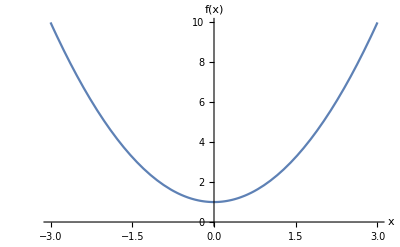

```mathematica
Plot[f[x],{x,-3,3},AxesLabel->{x,"f(x)"}]
```

```mathematica
Roots[f[x]==0,x]
```

x==ⅈ||x==-ⅈ

```mathematica
I
```

ⅈ

```mathematica
f[I]
```

0

```mathematica
f[-I]
```

0

```mathematica
perm=Permutations[{1,2,3,4}]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
Length[perm]
```

24

```mathematica
4!
```

24

```mathematica
myStirling[n_]:=√(2 π  n)(n/E)^n
```

```mathematica
myStirling[4] //N
```

23.5062

```mathematica
4!
```

24

```mathematica
Table[{n,(n!)/myStirling[n]//N},{n,1,20}] //TableForm
```

1 | 1.08444
2 | 1.04221
3 | 1.02806
4 | 1.02101
5 | 1.01678
6 | 1.01397
7 | 1.01197
8 | 1.01047
9 | 1.0093
10 | 1.00837
11 | 1.0076
12 | 1.00697
13 | 1.00643
14 | 1.00597
15 | 1.00557
16 | 1.00522
17 | 1.00491
18 | 1.00464
19 | 1.0044
20 | 1.00418

```mathematica
2.3! (*It did Gamma of 3.3*)
```

2.68344

```mathematica
Gamma[3.3]
```

2.68344

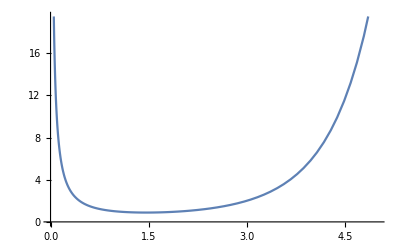

```mathematica
Plot[Gamma[x],{x,0,5}]
```

```mathematica
Gamma[5]
```

24